```mathematica
fileStream = OpenRead["/Users/katjad/Documents/iNaturalist/0010107-200613084148143.csv"]
```

InputStream[…]

```mathematica
StreamPosition[fileStream]
```

0

```mathematica
line=ReadLine[fileStream]
```

gbifID	datasetKey	occurrenceID	kingdom	phylum	class	order	family	genus	species	infraspecificEpithet	taxonRank	scientificName	verbatimScientificName	verbatimScientificNameAuthorship	countryCode	locality	stateProvince	occurrenceStatus	individualCount	publishingOrgKey	decimalLatitude	decimalLongitude	coordinateUncertaintyInMeters	coordinatePrecision	elevation	elevationAccuracy	depth	depthAccuracy	eventDate	day	month	year	taxonKey	speciesKey	basisOfRecord	institutionCode	collectionCode	catalogNumber	recordNumber	identifiedBy	dateIdentified	license	rightsHolder	recordedBy	typeStatus	establishmentMeans	lastInterpreted	mediaType	issue

```mathematica
headings =StringSplit[line,"\t"];
Position[headings,"recordedBy"]
Position[headings,"identifiedBy"]
```

{{45}}

{{41}}

```mathematica
Dynamic[n]
```

```mathematica
submitterCountsByMonth = <||>;
recorderCountsByMonth = <||>;
recorderIDs = <||>;
submitterIDs = <||>;
n = 0;
Module[{line,lineList,date,recorder, submitter},
	While[line=ReadLine[fileStream];line =!= EndOfFile,
		n++;
		lineList = StringSplit[line,"\t"];
		date= StringTake[lineList[[30]],7];
		recorder = lineList[[45]];
		submitter = lineList[[41]];
		
		If[
			!KeyExistsQ[recorderIDs,date],
			recorderCountsByMonth[date]=1;
			recorderIDs[date]={recorder},
			If[
				MemberQ[recorderIDs[date],recorder],
				Nothing,
				Append[recorderIDs[date],recorder];
				recorderCountsByMonth[date]++]];
					
		If[
			!KeyExistsQ[submitterIDs,date],
			submitterCountsByMonth[date]=1;
			submitterIDs[date]={recorder},
			If[
				MemberQ[submitterIDs[date],recorder],
				Nothing,
				Append[submitterIDs[date],recorder];
				submitterCountsByMonth[date]++]]
		]
	];
Close[fileStream];
```

StringTake::take: Cannot take positions 1 through 7 in "".

General::stop: Further output of StringTake::take will be suppressed during this calculation.

```mathematica
(*Export["/Users/katjad/Documents/iNaturalist/submitterCountsByMonth.mx",submitterCountsByMonth];
Export["/Users/katjad/Documents/iNaturalist/recorderCountsByMonth.mx",recorderCountsByMonth];*)
```

```mathematica
dateCounts = <||>;
n = 0;
Module[{line,date},
	While[line=ReadLine[fileStream];line =!= EndOfFile,
		n++;
		date= StringTake[StringSplit[line,"\t"][[30]],10];
		If[
			!KeyExistsQ[dateCounts,date],
			dateCounts[date]=1,
			dateCounts[date]++]
		]
	];
Close[fileStream];
```

StringTake::take: Cannot take positions 1 through 10 in "".

General::stop: Further output of StringTake::take will be suppressed during this calculation.

```mathematica
dateCounts
```

<|2011-05-01→627,2011-08-11→500,2010-01-14→159,2012-05-05→1093,2012-06-02→1193,2012-07-15→994,2009-07-08→310,2012-10-09→371,2012-11-16→452,1980-08-24→4,14476,1958-06-06→1,1980-06-21→1,1974-05-27→1,1976-03-16→1,1996-01-07→1,1958-08-11→1,1997-10-02→1,1990-06-04→1,1994-12-27→1|>
 |  |  |  |

```mathematica
dateCounts["2020-06-01"]
```

25253

```mathematica
exampleLine=StringSplit[ReadLine[fileStream],"\t"];
StringTake[exampleLine[[30]],10]
```

2019-04-01

```mathematica
DateObject["2014-05-24T13:17:00","Day"]
```

Day: Sat 24 May 2014

```mathematica
Close[fileStream]
```

/Users/katjad/Documents/iNaturalist/0010107-200613084148143.csv

```mathematica
(*Export["~/Documents/iNaturalist/dateCounts.mx",dateCounts]*)
```

~/Documents/iNaturalist/dateCounts.mx

```mathematica
tsAssoc=KeyMap[DateObject,KeySelect[dateCounts,StringQ]];
```

```mathematica
ts=TimeSeries[tsAssoc,MissingDataMethod->MissingDataMethod->{"Constant",0}]
```

TimeSeries[…]

```mathematica
tsClipped=TimeSeriesWindow[ts,{DateObject[{2008,1,1}],InfiniteFuture}]
```

TimeSeries[…]

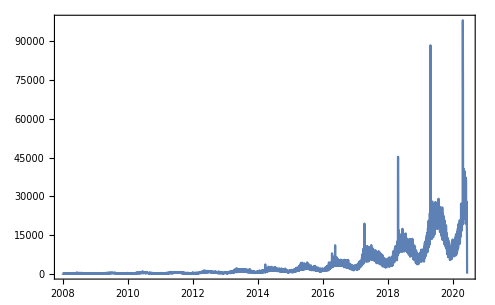

```mathematica
DateListPlot[tsClipped,PlotRange->All]
```

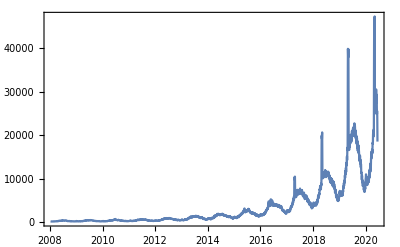

```mathematica
DateListPlot[MovingMap[Mean,tsClipped,Quantity[10, "Days"]],PlotRange->All]
```

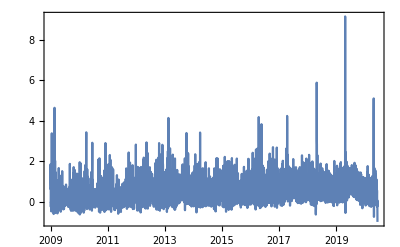

```mathematica
DateListPlot[MovingMap[(Last[#]-First[#])/First[#]&,tsClipped,"Year"],PlotRange->All]
```

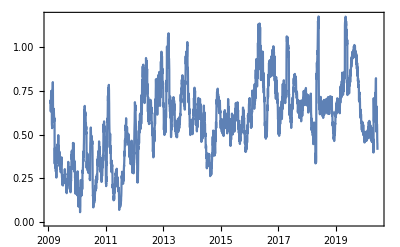

```mathematica
DateListPlot[MovingMap[Mean,MovingMap[(Last[#]-First[#])/First[#]&,tsClipped,"Year"],Quantity[30, "Days"]],PlotRange->All]
```

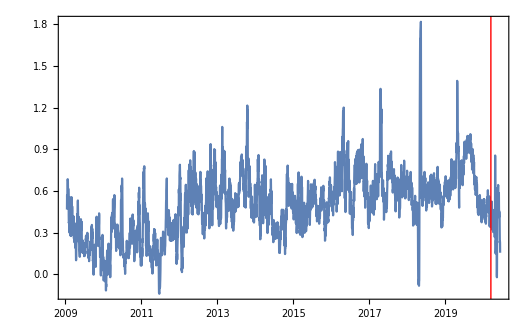

```mathematica
DateListPlot[MovingMap[(Last[#]-First[#])/First[#]&,MovingMap[Mean,tsClipped,Quantity[15, "Days"]],"Year"],Epilog->{Red,InfiniteLine[{DateObject[{2020,3,15}],0},{0,1}]},PlotRange->All]
```

```mathematica
Replace[submitterCountsByMonth
```

```mathematica
Flatten[Table[Table[StringJoin[ToString[x],"-",y],{y,{"01","02","03","04","05","06","07","08","09","10","11","12"}}],{x,2017,2020,1}]]
```

{2017-01,2017-02,2017-03,2017-04,2017-05,2017-06,2017-07,2017-08,2017-09,2017-10,2017-11,2017-12,2018-01,2018-02,2018-03,2018-04,2018-05,2018-06,2018-07,2018-08,2018-09,2018-10,2018-11,2018-12,2019-01,2019-02,2019-03,2019-04,2019-05,2019-06,2019-07,2019-08,2019-09,2019-10,2019-11,2019-12,2020-01,2020-02,2020-03,2020-04,2020-05,2020-06,2020-07,2020-08,2020-09,2020-10,2020-11,2020-12}

```mathematica
submitterCountsByMonth
```

<|2011-05→14280,2011-08→15472,2010-01→5197,2012-05→23694,2012-06→25004,2012-07→25973,2009-07→12377,2012-10→14025,2012-11→12794,1980-08→47,2013-01→13407,2013-02→14983,2013-03→20568,2009-05→9888,2013-04→28747,2013-05→34145,2013-06→37688,2005-10→1606,2013-07→40083,2013-08→37333,2013-09→28781,2013-10→26581,2013-11→20273,2012-03→12806,2014-01→22345,2014-02→21240,2014-03→32261,2010-11→6095,2014-04→40155,2012-12→12917,2014-05→53840,2014-06→49414,2014-07→52584,2014-08→47691,2014-09→39669,2014-10→36933,2009-11→4819,2014-11→32440,2014-12→27225,2015-01→32721,2007-02→2290,2015-02→31921,2015-03→45555,2015-04→58096,2015-05→80455,2015-06→76224,2015-07→84269,2015-08→68031,2015-09→59921,2010-06→15906,2015-10→53662,2011-03→8314,2015-11→46018,2011-09→11339,2015-12→44411,2016-01→50471,2016-02→53961,2005-05→3410,2007-04→3999,2016-03→77871,2016-04→115476,2016-05→132664,2016-06→127085,2016-07→123575,2011-01→7542,2016-08→115699,2012-04→18611,2016-09→107708,2011-10→9434,2010-09→8387,2016-10→100197,2016-11→74655,2016-12→66708,2017-01→77569,2017-02→83087,2017-03→128414,1979-05→65,2017-04→229601,2017-05→198344,2017-06→205909,2005-02→936,2017-07→221653,2011-07→16614,2017-08→190783,2010-03→7105,2004-11→1141,2017-09→173607,2017-10→153174,2003-07→1929,2017-11→124782,2017-12→107698,2010-07→13545,2018-01→125587,2006-07→5907,2006-12→2068,2018-02→121319,2018-03→193744,2018-04→366548,2008-12→3966,2006-01→2437,2009-12→4320,2018-05→325748,2005-08→3173,2018-06→335798,2009-08→9829,2018-07→346587,2011-11→7808,2007-01→2614,2018-08→306984,2010-05→12651,2018-09→283703,2007-07→8292,2008-05→7821,1975-07→17,2018-10→248181,2007-08→6454,2018-11→185011,2007-10→4489,2018-12→174847,2008-04→5190,2008-10→4535,2019-01→202207,2002-12→379,2019-02→202689,2007-06→6533,2019-03→335334,2009-09→6543,2019-04→702151,2009-06→11298,2019-05→562148,2019-06→601874,2011-04→11682,2019-07→658188,2019-08→605810,2019-09→503216,2006-09→2771,2019-10→411567,2019-11→281299,2005-01→1416,2008-03→4319,2019-12→248660,2020-01→293147,2012-01→9622,1986-11→27,2005-06→3594,2010-08→11570,2008-08→8488,2020-02→319158,2008-11→3955,1993-05→90,2020-03→464459,2020-04→863084,2020-05→879574,2020-06→228894,2011-12→7799,2012-09→18601,2006-03→2131,2008-06→9709,2010-04→9715,2012-08→20812,2012-02→8633,2013-12→18710,2009-02→4255,2000-03→215,2009-04→7173,2008-02→2970,2008-09→5557,2010-02→4599,2007-05→5590,2011-02→6010,2004-01→919,2003-12→713,2002-01→359,2001-03→220,2005-09→1964,2006-06→4970,2008-07→9747,1988-08→264,1975-10→43,2010-12→5313,2000-08→446,2002-06→840,2007-12→3087,2006-08→4261,1998-08→175,2007-11→2881,1996-04→86,2002-03→343,2011-06→15944,2005-07→3744,2006-04→3807,2007-09→4205,2009-03→5451,2009-01→4971,1945-02→1,2005-12→1711,2006-05→4508,2004-07→2821,2010-10→7250,2001-12→253,2009-10→5644,1977-01→8,2004-12→1277,1983-09→30,2007-03→3449,1995-07→186,2002-10→760,2003-10→920,2003-06→1720,2004-06→2039,1971-09→5,2001-08→481,2002-05→826,2003-04→861,1997-09→177,1976-06→65,2001-11→240,1991-07→147,2005-11→1390,2003-08→1522,1980-07→130,1998-01→136,2003-05→1333,2003-09→1080,2003-02→480,1981-07→47,1986-12→68,2008-01→3336,2006-10→2564,2002-07→876,2004-04→1708,1944-01→1,1977-06→50,1986-07→64,2000-12→294,1999-08→319,2002-08→829,1977-07→53,2006-02→1883,2004-05→2271,2001-06→493,1998-09→139,1986-10→33,2005-03→1399,1981-01→18,1982-03→11,1998-06→325,1991-05→61,2004-08→2211,1992-03→67,1995-02→75,2003-11→781,1999-06→261,2000-05→347,1954-07→12,1990-01→44,1980-03→18,2002-04→424,2000-07→528,2005-04→2270,1999-10→91,1996-06→160,1995-04→181,1983-12→25,2004-03→997,1992-10→44,2004-02→809,1972-08→59,2001-05→390,1998-11→228,2003-03→597,1981-04→21,1996-02→60,1997-03→123,1992-05→119,1974-02→4,2002-09→620,2004-09→1343,1998-05→246,1977-10→21,1986-03→52,1989-07→84,1974-06→83,1986-09→37,1991-11→47,1997-12→36,2002-11→401,1992-04→147,1987-06→106,1993-10→46,1944-03→1,1980-01→611,2004-10→1305,1993-04→136,2000-01→785,1979-06→35,1971-07→18,1984-05→54,1999-04→171,1983-06→51,1992-06→87,1986-01→27,1990-12→25,1987-07→144,2006-11→2346,1984-07→63,1989-05→71,2003-01→478,1997-01→32,1996-08→170,2001-04→316,1988-12→25,2001-09→357,1994-01→49,1986-08→95,1999-07→383,1995-08→116,1997-06→277,1998-10→137,1996-11→59,2000-04→281,1984-06→90,1988-02→30,1999-02→113,1980-05→83,1973-06→66,1975-12→17,2001-07→459,1985-05→89,1986-06→88,1985-06→83,1990-07→146,1984-10→23,1989-12→43,1998-07→369,1943-11→1,1999-01→117,1994-06→110,1977-12→9,1981-11→3,1985-03→27,1988-09→63,1984-01→42,1997-07→179,1994-08→86,1979-01→18,1981-10→32,1998-03→93,1996-05→106,1992-08→166,2000-06→341,1974-07→27,2001-01→184,1997-04→80,1984-03→30,1979-04→47,1999-09→148,1965-08→6,1987-08→81,1974-08→63,1981-03→10,1996-12→47,1997-08→151,1970-05→10,1988-10→15,1994-02→28,1989-04→42,1973-08→56,1987-10→55,1988-05→182,1995-01→74,2001-02→185,1990-08→113,1994-09→76,1959-01→2,2000-02→193,1985-07→87,1977-08→32,2000-09→244,1993-12→18,1996-01→97,1990-05→122,1999-03→151,1983-05→40,1999-12→265,1972-09→6,1970-06→13,1982-09→26,1980-04→37,1991-08→89,1982-02→10,1991-02→27,1998-12→53,1982-07→60,1980-09→26,1985-10→23,1982-06→36,1981-08→47,1988-01→48,1983-01→10,1991-04→91,1988-04→78,1992-02→41,1989-11→85,2002-02→357,1982-08→68,1971-10→2,1986-04→59,1995-12→56,1982-04→31,2001-10→243,1987-09→81,1980-06→60,1985-09→29,1996-09→105,1999-11→230,1945-11→1,1973-07→56,1973-05→25,1978-05→33,1996-10→82,2000-11→149,1987-05→130,1986-05→83,1995-09→92,1951-07→2,1996-07→127,1938-05→2,1970-07→30,1971-08→18,1987-03→60,1993-08→64,1979-02→8,1944-08→2,1998-02→90,1983-04→21,1973-09→22,1976-01→37,1948-09→2,1991-09→43,1982-11→9,1978-08→68,1999-05→257,1964-07→4,1996-03→67,1967-10→1,1975-09→23,1995-05→230,1979-07→34,1987-12→32,1970-11→11,1978-12→17,1909-01→1,1985-04→66,1981-06→30,1984-08→66,1993-06→106,1987-04→103,1971-11→6,1995-10→43,1998-04→239,1940-01→1,1990-03→48,1990-06→76,1978-06→82,1994-07→90,1976-11→11,1979-09→45,1992-07→102,1992-11→85,1987-11→52,1969-07→25,1989-09→56,1977-09→48,2000-10→191,1976-07→35,1974-03→5,1973-03→7,1990-04→70,1993-07→100,1991-12→20,1993-01→60,1991-01→35,1977-05→47,1965-07→5,1966-07→4,1990-11→21,1991-10→42,1942-07→6,1975-06→60,1992-09→116,1994-05→103,1997-11→37,1972-10→20,1981-05→43,1991-06→108,1989-08→75,1993-03→83,1978-01→15,1925-01→1,1997-05→149,1962-10→2,1988-07→99,1993-02→51,1989-10→23,1991-03→72,1992-01→32,1983-10→18,1989-06→119,1987-01→32,1990-02→48,1971-05→17,1982-05→44,1976-05→36,1982-10→10,1949-04→1,1973-12→4,1978-07→84,1988-03→68,1995-06→141,1984-04→54,1927-01→1,1976-08→53,1970-03→4,1915-06→2,1979-03→12,1995-03→39,1967-06→8,1966-05→5,1979-08→41,1993-11→55,1959-07→4,1920-01→1,1994-03→52,1997-10→74,1997-02→58,1922-10→1,1978-04→30,1983-08→40,1946-08→1,1977-11→15,1982-12→6,1994-12→40,1945-07→1,1994-11→36,1988-06→112,1985-12→18,1943-09→2,1985-01→12,1964-06→7,1974-01→12,1989-01→13,1975-01→23,1980-11→29,1989-03→30,1975-04→13,1980-10→30,1958-04→5,1980-12→18,1952-05→2,1987-02→29,1973-04→10,1968-07→8,1950-06→1,1994-10→40,1975-03→15,1974-04→38,1962-11→1,1968-05→10,1945-03→1,1971-06→31,1976-03→17,1979-11→17,1924-03→1,1973-11→11,1965-06→9,1983-07→71,1985-08→45,1974-10→9,1939-06→1,1969-05→8,1977-04→32,1934-01→1,1938-01→1,1978-10→23,1977-02→9,1981-12→17,1980-02→40,1984-12→27,1964-04→4,1970-08→10,1978-09→36,1947-08→2,1979-10→9,1975-08→29,1976-04→47,1911-08→1,1961-08→1,1972-07→40,1904-05→1,1938-08→6,1972-11→9,1995-11→19,1985-11→13,1988-11→15,1972-01→8,1943-05→2,1978-03→25,1972-06→21,1984-02→5,1966-06→8,1933-07→1,1993-09→25,1954-06→7,1972-12→18,1994-04→69,1963-06→2,1974-09→6,1984-11→13,1984-09→33,1947-07→1,1942-05→1,1972-05→12,1990-09→61,1942-08→5,1981-09→18,1968-06→9,1957-08→2,1938-04→1,1955-01→2,1972-04→3,1952-04→1,1978-02→9,1978-11→8,1977-03→3,1975-02→46,1958-07→1,1983-03→14,1970-01→28,1945-05→1,1973-01→4,1940-07→1,1976-09→26,1964-10→3,1940-09→3,1967-12→2,1983-11→10,1949-08→3,1947-09→1,1970-09→4,1937-12→2,1969-09→1,1989-02→50,1981-02→6,1947-06→2,1937-10→1,1965-05→3,1968-09→4,1974-05→24,1990-10→24,1959-03→3,1969-12→4,1976-12→19,1969-01→2,1976-10→16,1971-04→15,1967-08→3,1897-12→1,1953-07→5,1944-10→1,1973-02→2,1957-03→1,1964-08→3,1971-02→5,1953-08→1,1949-05→2,1979-12→16,1949-07→2,1943-08→1,1942-04→1,1920-07→2,1986-02→11,1929-08→1,1938-07→1,1931-07→1,1930-06→2,1992-12→23,1948-06→1,1952-07→2,1975-05→22,1930-04→1,1955-07→6,1973-10→3,1939-09→1,1964-02→2,1946-04→1,1968-04→5,1970-12→4,1951-06→2,1970-10→8,1972-02→5,1974-11→4,1953-06→1,1947-04→1,1946-05→3,1962-12→1,1925-09→1,1963-10→1,1942-01→1,1926-01→1,1970-04→12,1952-08→2,1933-02→1,1968-08→8,1966-03→2,1912-05→2,1969-10→2,1941-07→3,1965-11→2,1971-12→3,1928-12→1,1960-04→1,1939-01→1,1958-12→2,1958-08→3,1967-01→1,1949-06→7,1938-06→1,1919-01→1,1956-06→1,1960-06→5,1901-12→1,StringTake[,7]→4,1972-03→4,1957-06→2,1938-12→4,1922-01→1,1920-03→1,1946-10→1,1944-02→1,1942-06→1,1966-04→1,1983-02→8,1932-08→1,1928-01→1,1954-01→1,1931-01→2,1966-10→4,1926-08→1,1939-04→1,1959-06→5,1934-11→1,1963-07→1,1982-01→11,1966-09→2,1952-06→4,1971-01→19,1921-11→2,1920-12→1,1922-07→1,1960-01→1,1963-08→1,1966-01→2,1966-02→3,1969-08→3,1964-11→1,1967-05→4,1985-02→10,1949-01→2,1963-01→1,1974-12→6,1945-08→1,1953-03→1,1967-04→3,1946-06→2,1948-10→1,1926-07→1,1929-01→1,1969-06→15,1921-01→1,1956-01→1,1958-06→3,1949-11→1,1950-11→2,1941-08→1,1967-03→2,1965-01→1,1910-11→1,1948-07→2,1946-12→1,1966-08→5,1910-05→1,1956-08→2,1931-04→1,1958-01→1,1931-11→1,1907-03→1,1944-04→1,1954-04→1,1935-06→1,1969-04→4,1956-11→1,1975-11→1,1967-07→2,1946-09→1,1948-08→1,1960-08→4,1961-02→1,1949-10→1,1923-01→1,1971-03→4,1965-09→1,1941-05→1,1963-03→1,1964-01→2,1960-05→2,1976-02→4,1947-05→2,1934-07→4,1964-09→4,1914-10→2,1916-10→1,1941-06→2,1948-03→1,1920-08→1,1937-06→1,1917-12→1,1936-02→1,1966-12→2,1944-05→1,1959-12→2,1939-10→1,1950-07→1,1962-01→1,1928-08→1,1956-09→1,1943-06→4,1937-07→2,1968-12→2,1932-07→1,1959-08→3,1948-02→1,1965-04→1,1941-02→1,1931-06→1,1928-05→2,1930-01→1,1956-02→1,1949-03→2,1915-05→1,1924-12→1,1952-09→1,1923-12→1,1941-04→1,1947-10→1,1914-09→1,1965-03→1,1946-07→3,1934-04→1,1936-01→1,1960-11→1,1929-11→1,1968-03→2,1936-10→1,1939-05→1,1955-12→1,1923-09→1,1935-08→1,1951-09→1,1969-03→1,1968-01→1,1949-12→1,1951-10→1,1913-05→1,1963-04→1,1944-07→2,1934-05→1,1932-02→1,1906-01→1,1934-06→1,1955-06→4,1962-06→1,1953-09→2,1963-09→1,1955-03→1,1940-11→1,1961-07→2,1949-09→1,1967-09→1,1954-03→1,1951-08→2,1929-04→1,1946-03→1,1900-03→1,1924-01→1,1950-09→2,1917-10→1,1940-02→1,1953-05→1,1916-11→1,1915-03→1,1932-01→1,1922-02→1,1967-02→1,1870-01→1,1962-08→1,1937-03→1,1961-10→2,1954-11→1,1936-06→1,1951-03→1,1916-01→1,1904-01→1,1965-10→1,1956-07→2,1957-11→1,1917-07→1,1948-05→3,1940-06→1,1943-07→2,1915-08→1,1960-07→1,1936-08→1,1913-07→1,1919-05→1,1839-01→1,1962-04→1,1953-01→1,1934-09→1,1903-08→1,1950-05→1,1911-10→1,1962-09→1,1917-02→1,1944-06→1,1961-11→1,1942-11→1,1935-07→1|>

## Weekly

```mathematica
fileStream = OpenRead["/Users/katjad/Documents/iNaturalist/0010107-200613084148143.csv"]
```

InputStream[…]

```mathematica
StreamPosition[fileStream]
```

0

```mathematica
line=ReadLine[fileStream]
```

gbifID	datasetKey	occurrenceID	kingdom	phylum	class	order	family	genus	species	infraspecificEpithet	taxonRank	scientificName	verbatimScientificName	verbatimScientificNameAuthorship	countryCode	locality	stateProvince	occurrenceStatus	individualCount	publishingOrgKey	decimalLatitude	decimalLongitude	coordinateUncertaintyInMeters	coordinatePrecision	elevation	elevationAccuracy	depth	depthAccuracy	eventDate	day	month	year	taxonKey	speciesKey	basisOfRecord	institutionCode	collectionCode	catalogNumber	recordNumber	identifiedBy	dateIdentified	license	rightsHolder	recordedBy	typeStatus	establishmentMeans	lastInterpreted	mediaType	issue

```mathematica
getWeek[do_?DateObjectQ]:=Floor[(UnixTime[do]-UnixTime[DateObject[{DateValue[do,"Year"],1,1}]])/(7*24*60*60)]
```

```mathematica
Now
```

Sun 28 Jun 2020 19:52:57GMT-4.

```mathematica
submitterCountsByWeek = <||>;
recorderCountsByWeek = <||>;
recorderIDs = <||>;
submitterIDs = <||>;
n = 0;
Module[{line,lineList,exactDate,date,recorder, submitter},
	While[line=ReadLine[fileStream];line =!= EndOfFile,
		n++;
		lineList = StringSplit[line,"\t"];
		exactDate = DateObject[StringTake[lineList[[30]],10],"Week"];
		date = {DateValue[exactDate,"Year"], getWeek[exactDate]};
		recorder = lineList[[45]];
		submitter = lineList[[41]];
		
		If[
			!KeyExistsQ[recorderIDs,date],
			recorderCountsByWeek[date]=1;
			recorderIDs[date]={recorder},
			If[
				MemberQ[recorderIDs[date],recorder],
				Nothing,
				Append[recorderIDs[date],recorder];
				recorderCountsByWeek[date]++]];
					
		If[
			!KeyExistsQ[submitterIDs,date],
			submitterCountsByWeek[date]=1;
			submitterIDs[date]={recorder},
			If[
				MemberQ[submitterIDs[date],recorder],
				Nothing,
				Append[submitterIDs[date],recorder];
				submitterCountsByWeek[date]++]]
		]
	];
Close[fileStream];
```

$Aborted

```mathematica
Now
```

Sun 28 Jun 2020 18:45:20GMT-4.

```mathematica
Dynamic[Column[{n,ProgressIndicator[n,{0,16699363}]}]]
```

```mathematica
Export["~/Documents/iNaturalist/submitterCountsByWeek.mx",submitterCountsByWeek];
Export["~/Documents/iNaturalist/recorderCountsByDay.mx",recorderCountsByWeek];
```

```mathematica
DateListPlot[submitterCountsByWeek]
```

```mathematica
weekts=TimeSeries[KeySelect[submitterCountsByWeek,DateObjectQ],MissingDataMethod->{"Constant",0}]
```

TimeSeries[…]

```mathematica
weekTsClipped=TimeSeriesWindow[weekts,{DateObject[{2008,1,1}],InfiniteFuture}]
```

TimeSeries[…]

```mathematica
Normal[weekTsClipped][[;;5]]
```

{{Tue 1 Jan 2008 00:00:00GMT-4.,206},{Wed 2 Jan 2008 00:00:00GMT-4.,82},{Thu 3 Jan 2008 00:00:00GMT-4.,97},{Fri 4 Jan 2008 00:00:00GMT-4.,119},{Sat 5 Jan 2008 00:00:00GMT-4.,128}}

```mathematica
KeySelect[submitterCountsByWeek,DateObjectQ][[;;10]]
```

<|Week beginning: Mon 25 Apr 2011→609,Week beginning: Mon 8 Aug 2011→498,Week beginning: Mon 11 Jan 2010→156,Week beginning: Mon 30 Apr 2012→1025,Week beginning: Mon 28 May 2012→1176,Week beginning: Mon 9 Jul 2012→993,Week beginning: Mon 6 Jul 2009→307,Week beginning: Mon 8 Oct 2012→371,Week beginning: Mon 12 Nov 2012→438,Week beginning: Mon 18 Aug 1980→4|>

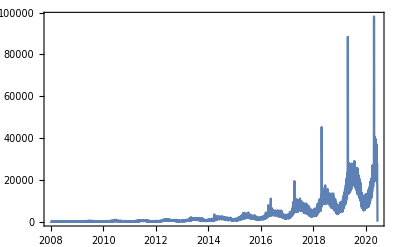

```mathematica
DateListPlot[weekTsClipped,PlotRange->All]
```

```mathematica
Values[GroupBy[Normal[weekTsClipped],DateValue[#[[1]],"Year"]&]][[2]]
```

{{Thu 1 Jan 2009 00:00:00GMT-4.,323},{Fri 2 Jan 2009 00:00:00GMT-4.,242},{Sat 3 Jan 2009 00:00:00GMT-4.,201},{Sun 4 Jan 2009 00:00:00GMT-4.,197},{Mon 5 Jan 2009 00:00:00GMT-4.,91},{Tue 6 Jan 2009 00:00:00GMT-4.,105},{Wed 7 Jan 2009 00:00:00GMT-4.,82},{Thu 8 Jan 2009 00:00:00GMT-4.,147},{Fri 9 Jan 2009 00:00:00GMT-4.,101},{Sat 10 Jan 2009 00:00:00GMT-4.,102},{Sun 11 Jan 2009 00:00:00GMT-4.,222},{Mon 12 Jan 2009 00:00:00GMT-4.,73},{Tue 13 Jan 2009 00:00:00GMT-4.,185},{Wed 14 Jan 2009 00:00:00GMT-4.,138},{Thu 15 Jan 2009 00:00:00GMT-4.,234},{Fri 16 Jan 2009 00:00:00GMT-4.,130},{Sat 17 Jan 2009 00:00:00GMT-4.,300},{Sun 18 Jan 2009 00:00:00GMT-4.,210},{Mon 19 Jan 2009 00:00:00GMT-4.,130},{Tue 20 Jan 2009 00:00:00GMT-4.,100},{Wed 21 Jan 2009 00:00:00GMT-4.,85},{Thu 22 Jan 2009 00:00:00GMT-4.,135},{Fri 23 Jan 2009 00:00:00GMT-4.,81},{Sat 24 Jan 2009 00:00:00GMT-4.,180},{Sun 25 Jan 2009 00:00:00GMT-4.,180},{Mon 26 Jan 2009 00:00:00GMT-4.,121},{Tue 27 Jan 2009 00:00:00GMT-4.,134},{Wed 28 Jan 2009 00:00:00GMT-4.,118},{Thu 29 Jan 2009 00:00:00GMT-4.,78},{Fri 30 Jan 2009 00:00:00GMT-4.,144},{Sat 31 Jan 2009 00:00:00GMT-4.,215},{Sun 1 Feb 2009 00:00:00GMT-4.,190},{Mon 2 Feb 2009 00:00:00GMT-4.,113},{Tue 3 Feb 2009 00:00:00GMT-4.,138},{Wed 4 Feb 2009 00:00:00GMT-4.,71},{Thu 5 Feb 2009 00:00:00GMT-4.,81},{Fri 6 Feb 2009 00:00:00GMT-4.,112},{Sat 7 Feb 2009 00:00:00GMT-4.,230},{Sun 8 Feb 2009 00:00:00GMT-4.,182},{Mon 9 Feb 2009 00:00:00GMT-4.,120},{Tue 10 Feb 2009 00:00:00GMT-4.,74},{Wed 11 Feb 2009 00:00:00GMT-4.,97},{Thu 12 Feb 2009 00:00:00GMT-4.,122},{Fri 13 Feb 2009 00:00:00GMT-4.,99},{Sat 14 Feb 2009 00:00:00GMT-4.,214},{Sun 15 Feb 2009 00:00:00GMT-4.,172},{Mon 16 Feb 2009 00:00:00GMT-4.,135},{Tue 17 Feb 2009 00:00:00GMT-4.,127},{Wed 18 Feb 2009 00:00:00GMT-4.,143},{Thu 19 Feb 2009 00:00:00GMT-4.,148},{Fri 20 Feb 2009 00:00:00GMT-4.,119},{Sat 21 Feb 2009 00:00:00GMT-4.,298},{Sun 22 Feb 2009 00:00:00GMT-4.,245},{Mon 23 Feb 2009 00:00:00GMT-4.,66},{Tue 24 Feb 2009 00:00:00GMT-4.,96},{Wed 25 Feb 2009 00:00:00GMT-4.,126},{Thu 26 Feb 2009 00:00:00GMT-4.,99},{Fri 27 Feb 2009 00:00:00GMT-4.,143},{Sat 28 Feb 2009 00:00:00GMT-4.,237},{Sun 1 Mar 2009 00:00:00GMT-4.,246},{Mon 2 Mar 2009 00:00:00GMT-4.,73},{Tue 3 Mar 2009 00:00:00GMT-4.,77},{Wed 4 Mar 2009 00:00:00GMT-4.,89},{Thu 5 Mar 2009 00:00:00GMT-4.,133},{Fri 6 Mar 2009 00:00:00GMT-4.,165},{Sat 7 Mar 2009 00:00:00GMT-4.,230},{Sun 8 Mar 2009 00:00:00GMT-4.,227},{Mon 9 Mar 2009 00:00:00GMT-4.,173},{Tue 10 Mar 2009 00:00:00GMT-4.,126},{Wed 11 Mar 2009 00:00:00GMT-4.,92},{Thu 12 Mar 2009 00:00:00GMT-4.,123},{Fri 13 Mar 2009 00:00:00GMT-4.,115},{Sat 14 Mar 2009 00:00:00GMT-4.,216},{Sun 15 Mar 2009 00:00:00GMT-4.,276},{Mon 16 Mar 2009 00:00:00GMT-4.,110},{Tue 17 Mar 2009 00:00:00GMT-4.,149},{Wed 18 Mar 2009 00:00:00GMT-4.,130},{Thu 19 Mar 2009 00:00:00GMT-4.,171},{Fri 20 Mar 2009 00:00:00GMT-4.,139},{Sat 21 Mar 2009 00:00:00GMT-4.,312},{Sun 22 Mar 2009 00:00:00GMT-4.,250},{Mon 23 Mar 2009 00:00:00GMT-4.,126},{Tue 24 Mar 2009 00:00:00GMT-4.,101},{Wed 25 Mar 2009 00:00:00GMT-4.,161},{Thu 26 Mar 2009 00:00:00GMT-4.,179},{Fri 27 Mar 2009 00:00:00GMT-4.,159},{Sat 28 Mar 2009 00:00:00GMT-4.,287},{Sun 29 Mar 2009 00:00:00GMT-4.,231},{Mon 30 Mar 2009 00:00:00GMT-4.,98},{Tue 31 Mar 2009 00:00:00GMT-4.,145},{Wed 1 Apr 2009 00:00:00GMT-4.,168},{Thu 2 Apr 2009 00:00:00GMT-4.,90},{Fri 3 Apr 2009 00:00:00GMT-4.,103},{Sat 4 Apr 2009 00:00:00GMT-4.,276},{Sun 5 Apr 2009 00:00:00GMT-4.,297},{Mon 6 Apr 2009 00:00:00GMT-4.,181},{Tue 7 Apr 2009 00:00:00GMT-4.,136},{Wed 8 Apr 2009 00:00:00GMT-4.,176},{Thu 9 Apr 2009 00:00:00GMT-4.,236},{Fri 10 Apr 2009 00:00:00GMT-4.,246},{Sat 11 Apr 2009 00:00:00GMT-4.,264},{Sun 12 Apr 2009 00:00:00GMT-4.,253},{Mon 13 Apr 2009 00:00:00GMT-4.,208},{Tue 14 Apr 2009 00:00:00GMT-4.,153},{Wed 15 Apr 2009 00:00:00GMT-4.,140},{Thu 16 Apr 2009 00:00:00GMT-4.,237},{Fri 17 Apr 2009 00:00:00GMT-4.,273},{Sat 18 Apr 2009 00:00:00GMT-4.,369},{Sun 19 Apr 2009 00:00:00GMT-4.,361},{Mon 20 Apr 2009 00:00:00GMT-4.,173},{Tue 21 Apr 2009 00:00:00GMT-4.,192},{Wed 22 Apr 2009 00:00:00GMT-4.,284},{Thu 23 Apr 2009 00:00:00GMT-4.,265},{Fri 24 Apr 2009 00:00:00GMT-4.,277},{Sat 25 Apr 2009 00:00:00GMT-4.,387},{Sun 26 Apr 2009 00:00:00GMT-4.,342},{Mon 27 Apr 2009 00:00:00GMT-4.,153},{Tue 28 Apr 2009 00:00:00GMT-4.,178},{Wed 29 Apr 2009 00:00:00GMT-4.,216},{Thu 30 Apr 2009 00:00:00GMT-4.,257},{Fri 1 May 2009 00:00:00GMT-4.,329},{Sat 2 May 2009 00:00:00GMT-4.,387},{Sun 3 May 2009 00:00:00GMT-4.,429},{Mon 4 May 2009 00:00:00GMT-4.,253},{Tue 5 May 2009 00:00:00GMT-4.,186},{Wed 6 May 2009 00:00:00GMT-4.,274},{Thu 7 May 2009 00:00:00GMT-4.,236},{Fri 8 May 2009 00:00:00GMT-4.,313},{Sat 9 May 2009 00:00:00GMT-4.,415},{Sun 10 May 2009 00:00:00GMT-4.,412},{Mon 11 May 2009 00:00:00GMT-4.,176},{Tue 12 May 2009 00:00:00GMT-4.,208},{Wed 13 May 2009 00:00:00GMT-4.,199},{Thu 14 May 2009 00:00:00GMT-4.,203},{Fri 15 May 2009 00:00:00GMT-4.,349},{Sat 16 May 2009 00:00:00GMT-4.,403},{Sun 17 May 2009 00:00:00GMT-4.,427},{Mon 18 May 2009 00:00:00GMT-4.,274},{Tue 19 May 2009 00:00:00GMT-4.,183},{Wed 20 May 2009 00:00:00GMT-4.,239},{Thu 21 May 2009 00:00:00GMT-4.,313},{Fri 22 May 2009 00:00:00GMT-4.,343},{Sat 23 May 2009 00:00:00GMT-4.,469},{Sun 24 May 2009 00:00:00GMT-4.,415},{Mon 25 May 2009 00:00:00GMT-4.,298},{Tue 26 May 2009 00:00:00GMT-4.,274},{Wed 27 May 2009 00:00:00GMT-4.,220},{Thu 28 May 2009 00:00:00GMT-4.,309},{Fri 29 May 2009 00:00:00GMT-4.,310},{Sat 30 May 2009 00:00:00GMT-4.,444},{Sun 31 May 2009 00:00:00GMT-4.,341},{Mon 1 Jun 2009 00:00:00GMT-4.,291},{Tue 2 Jun 2009 00:00:00GMT-4.,312},{Wed 3 Jun 2009 00:00:00GMT-4.,329},{Thu 4 Jun 2009 00:00:00GMT-4.,303},{Fri 5 Jun 2009 00:00:00GMT-4.,264},{Sat 6 Jun 2009 00:00:00GMT-4.,481},{Sun 7 Jun 2009 00:00:00GMT-4.,484},{Mon 8 Jun 2009 00:00:00GMT-4.,421},{Tue 9 Jun 2009 00:00:00GMT-4.,392},{Wed 10 Jun 2009 00:00:00GMT-4.,336},{Thu 11 Jun 2009 00:00:00GMT-4.,339},{Fri 12 Jun 2009 00:00:00GMT-4.,407},{Sat 13 Jun 2009 00:00:00GMT-4.,463},{Sun 14 Jun 2009 00:00:00GMT-4.,560},{Mon 15 Jun 2009 00:00:00GMT-4.,262},{Tue 16 Jun 2009 00:00:00GMT-4.,358},{Wed 17 Jun 2009 00:00:00GMT-4.,301},{Thu 18 Jun 2009 00:00:00GMT-4.,346},{Fri 19 Jun 2009 00:00:00GMT-4.,265},{Sat 20 Jun 2009 00:00:00GMT-4.,483},{Sun 21 Jun 2009 00:00:00GMT-4.,439},{Mon 22 Jun 2009 00:00:00GMT-4.,283},{Tue 23 Jun 2009 00:00:00GMT-4.,302},{Wed 24 Jun 2009 00:00:00GMT-4.,296},{Thu 25 Jun 2009 00:00:00GMT-4.,315},{Fri 26 Jun 2009 00:00:00GMT-4.,339},{Sat 27 Jun 2009 00:00:00GMT-4.,471},{Sun 28 Jun 2009 00:00:00GMT-4.,380},{Mon 29 Jun 2009 00:00:00GMT-4.,312},{Tue 30 Jun 2009 00:00:00GMT-4.,313},{Wed 1 Jul 2009 00:00:00GMT-4.,366},{Thu 2 Jul 2009 00:00:00GMT-4.,367},{Fri 3 Jul 2009 00:00:00GMT-4.,467},{Sat 4 Jul 2009 00:00:00GMT-4.,513},{Sun 5 Jul 2009 00:00:00GMT-4.,466},{Mon 6 Jul 2009 00:00:00GMT-4.,305},{Tue 7 Jul 2009 00:00:00GMT-4.,366},{Wed 8 Jul 2009 00:00:00GMT-4.,307},{Thu 9 Jul 2009 00:00:00GMT-4.,486},{Fri 10 Jul 2009 00:00:00GMT-4.,440},{Sat 11 Jul 2009 00:00:00GMT-4.,457},{Sun 12 Jul 2009 00:00:00GMT-4.,480},{Mon 13 Jul 2009 00:00:00GMT-4.,311},{Tue 14 Jul 2009 00:00:00GMT-4.,374},{Wed 15 Jul 2009 00:00:00GMT-4.,425},{Thu 16 Jul 2009 00:00:00GMT-4.,463},{Fri 17 Jul 2009 00:00:00GMT-4.,420},{Sat 18 Jul 2009 00:00:00GMT-4.,417},{Sun 19 Jul 2009 00:00:00GMT-4.,448},{Mon 20 Jul 2009 00:00:00GMT-4.,267},{Tue 21 Jul 2009 00:00:00GMT-4.,326},{Wed 22 Jul 2009 00:00:00GMT-4.,343},{Thu 23 Jul 2009 00:00:00GMT-4.,370},{Fri 24 Jul 2009 00:00:00GMT-4.,342},{Sat 25 Jul 2009 00:00:00GMT-4.,433},{Sun 26 Jul 2009 00:00:00GMT-4.,400},{Mon 27 Jul 2009 00:00:00GMT-4.,399},{Tue 28 Jul 2009 00:00:00GMT-4.,348},{Wed 29 Jul 2009 00:00:00GMT-4.,433},{Thu 30 Jul 2009 00:00:00GMT-4.,307},{Fri 31 Jul 2009 00:00:00GMT-4.,411},{Sat 1 Aug 2009 00:00:00GMT-4.,396},{Sun 2 Aug 2009 00:00:00GMT-4.,359},{Mon 3 Aug 2009 00:00:00GMT-4.,357},{Tue 4 Aug 2009 00:00:00GMT-4.,316},{Wed 5 Aug 2009 00:00:00GMT-4.,401},{Thu 6 Aug 2009 00:00:00GMT-4.,356},{Fri 7 Aug 2009 00:00:00GMT-4.,366},{Sat 8 Aug 2009 00:00:00GMT-4.,568},{Sun 9 Aug 2009 00:00:00GMT-4.,386},{Mon 10 Aug 2009 00:00:00GMT-4.,306},{Tue 11 Aug 2009 00:00:00GMT-4.,287},{Wed 12 Aug 2009 00:00:00GMT-4.,315},{Thu 13 Aug 2009 00:00:00GMT-4.,315},{Fri 14 Aug 2009 00:00:00GMT-4.,384},{Sat 15 Aug 2009 00:00:00GMT-4.,402},{Sun 16 Aug 2009 00:00:00GMT-4.,428},{Mon 17 Aug 2009 00:00:00GMT-4.,203},{Tue 18 Aug 2009 00:00:00GMT-4.,299},{Wed 19 Aug 2009 00:00:00GMT-4.,226},{Thu 20 Aug 2009 00:00:00GMT-4.,163},{Fri 21 Aug 2009 00:00:00GMT-4.,267},{Sat 22 Aug 2009 00:00:00GMT-4.,415},{Sun 23 Aug 2009 00:00:00GMT-4.,326},{Mon 24 Aug 2009 00:00:00GMT-4.,255},{Tue 25 Aug 2009 00:00:00GMT-4.,217},{Wed 26 Aug 2009 00:00:00GMT-4.,209},{Thu 27 Aug 2009 00:00:00GMT-4.,272},{Fri 28 Aug 2009 00:00:00GMT-4.,217},{Sat 29 Aug 2009 00:00:00GMT-4.,281},{Sun 30 Aug 2009 00:00:00GMT-4.,280},{Mon 31 Aug 2009 00:00:00GMT-4.,180},{Tue 1 Sep 2009 00:00:00GMT-4.,217},{Wed 2 Sep 2009 00:00:00GMT-4.,179},{Thu 3 Sep 2009 00:00:00GMT-4.,168},{Fri 4 Sep 2009 00:00:00GMT-4.,207},{Sat 5 Sep 2009 00:00:00GMT-4.,372},{Sun 6 Sep 2009 00:00:00GMT-4.,368},{Mon 7 Sep 2009 00:00:00GMT-4.,216},{Tue 8 Sep 2009 00:00:00GMT-4.,188},{Wed 9 Sep 2009 00:00:00GMT-4.,181},{Thu 10 Sep 2009 00:00:00GMT-4.,202},{Fri 11 Sep 2009 00:00:00GMT-4.,218},{Sat 12 Sep 2009 00:00:00GMT-4.,315},{Sun 13 Sep 2009 00:00:00GMT-4.,320},{Mon 14 Sep 2009 00:00:00GMT-4.,153},{Tue 15 Sep 2009 00:00:00GMT-4.,194},{Wed 16 Sep 2009 00:00:00GMT-4.,163},{Thu 17 Sep 2009 00:00:00GMT-4.,127},{Fri 18 Sep 2009 00:00:00GMT-4.,143},{Sat 19 Sep 2009 00:00:00GMT-4.,322},{Sun 20 Sep 2009 00:00:00GMT-4.,249},{Mon 21 Sep 2009 00:00:00GMT-4.,129},{Tue 22 Sep 2009 00:00:00GMT-4.,171},{Wed 23 Sep 2009 00:00:00GMT-4.,172},{Thu 24 Sep 2009 00:00:00GMT-4.,214},{Fri 25 Sep 2009 00:00:00GMT-4.,205},{Sat 26 Sep 2009 00:00:00GMT-4.,238},{Sun 27 Sep 2009 00:00:00GMT-4.,236},{Mon 28 Sep 2009 00:00:00GMT-4.,145},{Tue 29 Sep 2009 00:00:00GMT-4.,162},{Wed 30 Sep 2009 00:00:00GMT-4.,155},{Thu 1 Oct 2009 00:00:00GMT-4.,182},{Fri 2 Oct 2009 00:00:00GMT-4.,176},{Sat 3 Oct 2009 00:00:00GMT-4.,251},{Sun 4 Oct 2009 00:00:00GMT-4.,218},{Mon 5 Oct 2009 00:00:00GMT-4.,122},{Tue 6 Oct 2009 00:00:00GMT-4.,129},{Wed 7 Oct 2009 00:00:00GMT-4.,141},{Thu 8 Oct 2009 00:00:00GMT-4.,124},{Fri 9 Oct 2009 00:00:00GMT-4.,162},{Sat 10 Oct 2009 00:00:00GMT-4.,290},{Sun 11 Oct 2009 00:00:00GMT-4.,263},{Mon 12 Oct 2009 00:00:00GMT-4.,158},{Tue 13 Oct 2009 00:00:00GMT-4.,168},{Wed 14 Oct 2009 00:00:00GMT-4.,163},{Thu 15 Oct 2009 00:00:00GMT-4.,158},{Fri 16 Oct 2009 00:00:00GMT-4.,133},{Sat 17 Oct 2009 00:00:00GMT-4.,197},{Sun 18 Oct 2009 00:00:00GMT-4.,234},{Mon 19 Oct 2009 00:00:00GMT-4.,139},{Tue 20 Oct 2009 00:00:00GMT-4.,198},{Wed 21 Oct 2009 00:00:00GMT-4.,176},{Thu 22 Oct 2009 00:00:00GMT-4.,132},{Fri 23 Oct 2009 00:00:00GMT-4.,165},{Sat 24 Oct 2009 00:00:00GMT-4.,228},{Sun 25 Oct 2009 00:00:00GMT-4.,224},{Mon 26 Oct 2009 00:00:00GMT-4.,127},{Tue 27 Oct 2009 00:00:00GMT-4.,145},{Wed 28 Oct 2009 00:00:00GMT-4.,147},{Thu 29 Oct 2009 00:00:00GMT-4.,91},{Fri 30 Oct 2009 00:00:00GMT-4.,139},{Sat 31 Oct 2009 00:00:00GMT-4.,241},{Sun 1 Nov 2009 00:00:00GMT-4.,240},{Mon 2 Nov 2009 00:00:00GMT-4.,147},{Tue 3 Nov 2009 00:00:00GMT-4.,97},{Wed 4 Nov 2009 00:00:00GMT-4.,127},{Thu 5 Nov 2009 00:00:00GMT-4.,118},{Fri 6 Nov 2009 00:00:00GMT-4.,148},{Sat 7 Nov 2009 00:00:00GMT-4.,251},{Sun 8 Nov 2009 00:00:00GMT-4.,220},{Mon 9 Nov 2009 00:00:00GMT-4.,206},{Tue 10 Nov 2009 00:00:00GMT-4.,138},{Wed 11 Nov 2009 00:00:00GMT-4.,170},{Thu 12 Nov 2009 00:00:00GMT-4.,121},{Fri 13 Nov 2009 00:00:00GMT-4.,151},{Sat 14 Nov 2009 00:00:00GMT-4.,199},{Sun 15 Nov 2009 00:00:00GMT-4.,184},{Mon 16 Nov 2009 00:00:00GMT-4.,112},{Tue 17 Nov 2009 00:00:00GMT-4.,126},{Wed 18 Nov 2009 00:00:00GMT-4.,108},{Thu 19 Nov 2009 00:00:00GMT-4.,112},{Fri 20 Nov 2009 00:00:00GMT-4.,100},{Sat 21 Nov 2009 00:00:00GMT-4.,301},{Sun 22 Nov 2009 00:00:00GMT-4.,216},{Mon 23 Nov 2009 00:00:00GMT-4.,94},{Tue 24 Nov 2009 00:00:00GMT-4.,105},{Wed 25 Nov 2009 00:00:00GMT-4.,123},{Thu 26 Nov 2009 00:00:00GMT-4.,141},{Fri 27 Nov 2009 00:00:00GMT-4.,116},{Sat 28 Nov 2009 00:00:00GMT-4.,152},{Sun 29 Nov 2009 00:00:00GMT-4.,186},{Mon 30 Nov 2009 00:00:00GMT-4.,99},{Tue 1 Dec 2009 00:00:00GMT-4.,88},{Wed 2 Dec 2009 00:00:00GMT-4.,63},{Thu 3 Dec 2009 00:00:00GMT-4.,83},{Fri 4 Dec 2009 00:00:00GMT-4.,56},{Sat 5 Dec 2009 00:00:00GMT-4.,170},{Sun 6 Dec 2009 00:00:00GMT-4.,165},{Mon 7 Dec 2009 00:00:00GMT-4.,105},{Tue 8 Dec 2009 00:00:00GMT-4.,93},{Wed 9 Dec 2009 00:00:00GMT-4.,124},{Thu 10 Dec 2009 00:00:00GMT-4.,119},{Fri 11 Dec 2009 00:00:00GMT-4.,124},{Sat 12 Dec 2009 00:00:00GMT-4.,158},{Sun 13 Dec 2009 00:00:00GMT-4.,197},{Mon 14 Dec 2009 00:00:00GMT-4.,91},{Tue 15 Dec 2009 00:00:00GMT-4.,101},{Wed 16 Dec 2009 00:00:00GMT-4.,141},{Thu 17 Dec 2009 00:00:00GMT-4.,143},{Fri 18 Dec 2009 00:00:00GMT-4.,144},{Sat 19 Dec 2009 00:00:00GMT-4.,174},{Sun 20 Dec 2009 00:00:00GMT-4.,123},{Mon 21 Dec 2009 00:00:00GMT-4.,129},{Tue 22 Dec 2009 00:00:00GMT-4.,162},{Wed 23 Dec 2009 00:00:00GMT-4.,128},{Thu 24 Dec 2009 00:00:00GMT-4.,111},{Fri 25 Dec 2009 00:00:00GMT-4.,116},{Sat 26 Dec 2009 00:00:00GMT-4.,117},{Sun 27 Dec 2009 00:00:00GMT-4.,157},{Mon 28 Dec 2009 00:00:00GMT-4.,99},{Tue 29 Dec 2009 00:00:00GMT-4.,117},{Wed 30 Dec 2009 00:00:00GMT-4.,256},{Thu 31 Dec 2009 00:00:00GMT-4.,151}}

```mathematica
DateValue[#[[1]],"Week"]&/@Values[GroupBy[Normal[weekTsClipped],DateValue[#[[1]],"Year"]&]][[2]]
```

{1,1,1,1,2,2,2,2,2,2,2,3,3,3,3,3,3,3,4,4,4,4,4,4,4,5,5,5,5,5,5,5,6,6,6,6,6,6,6,7,7,7,7,7,7,7,8,8,8,8,8,8,8,9,9,9,9,9,9,9,10,10,10,10,10,10,10,11,11,11,11,11,11,11,12,12,12,12,12,12,12,13,13,13,13,13,13,13,14,14,14,14,14,14,14,15,15,15,15,15,15,15,16,16,16,16,16,16,16,17,17,17,17,17,17,17,18,18,18,18,18,18,18,19,19,19,19,19,19,19,20,20,20,20,20,20,20,21,21,21,21,21,21,21,22,22,22,22,22,22,22,23,23,23,23,23,23,23,24,24,24,24,24,24,24,25,25,25,25,25,25,25,26,26,26,26,26,26,26,27,27,27,27,27,27,27,28,28,28,28,28,28,28,29,29,29,29,29,29,29,30,30,30,30,30,30,30,31,31,31,31,31,31,31,32,32,32,32,32,32,32,33,33,33,33,33,33,33,34,34,34,34,34,34,34,35,35,35,35,35,35,35,36,36,36,36,36,36,36,37,37,37,37,37,37,37,38,38,38,38,38,38,38,39,39,39,39,39,39,39,40,40,40,40,40,40,40,41,41,41,41,41,41,41,42,42,42,42,42,42,42,43,43,43,43,43,43,43,44,44,44,44,44,44,44,45,45,45,45,45,45,45,46,46,46,46,46,46,46,47,47,47,47,47,47,47,48,48,48,48,48,48,48,49,49,49,49,49,49,49,50,50,50,50,50,50,50,51,51,51,51,51,51,51,52,52,52,52,52,52,52,53,53,53,53}

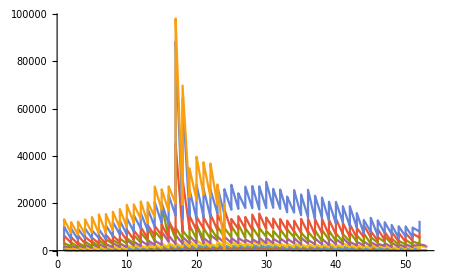

```mathematica
ListLinePlot[Values[SortBy[First]/@MapAt[DateValue[#,"Week"]&,GroupBy[Normal[weekTsClipped],DateValue[#[[1]],"Year"]&],{All,All,1}]],PlotRange->All]
```